# QEA Night 10

## Exercise

```mathematica
eq1 = θ[s]== Subscript[e, rr2][s]Subscript[G, P][s] Subscript[G, MC][s]Subscript[G, VC][s];
eq2 = Subscript[V, d][s] == Subscript[e, rr1][s] Subscript[G, PI][s];
eq3 = Subscript[e, rr1][s] == Subscript[θ, d][s] - θ[s] + Subscript[G, DC][s]V[s];
eq4 = V[s] == Subscript[e, rr2][s]Subscript[G, P][s]Subscript[G, MC][s];
eq5 = Subscript[e, rr2][s] == Subscript[V, d][s] - V[s];
sol = Solve[{eq1,eq2,eq3,eq4,eq5},{θ[s],Subscript[V, d][s],Subscript[e, rr1][s], V[s], Subscript[e, rr2][s]}][[1]];
{Subscript[G, TOTALSYSTEM][s]-> θ[s]/(Subscript[θ, d][s])/.sol} (* this is a rule to replace Subscript[G, TOTALSYSTEM], you can just extract the value by using the righthand side of the rule *)
trans = θ[s]/(Subscript[θ, d][s])/.sol/.{Subscript[G, PI][s]-> Subscript[K, p]+(Subscript[K, i]/s),Subscript[G, VC][s]-> -s/(L s^2- g),Subscript[G, MC][s]-> (a b )/(s+a),Subscript[G, P][s]-> Subscript[J, p]+(Subscript[J, i]/s), Subscript[G, DC][s]-> Subscript[K, t]/s}
tsumsub = Factor[trans /.{b->.003,a->8.3,L->.1,g->9.8}]
```

{G_TOTALSYSTEM[s]→(G_MC[s] G_P[s] G_PI[s] G_VC[s])/(1+G_MC[s] G_P[s]-G_DC[s] G_MC[s] G_P[s] G_PI[s]+G_MC[s] G_P[s] G_PI[s] G_VC[s])}

-((a b s (J_i/s+J_p) (K_i/s+K_p))/((a+s) (-g+L s^2) (1+(a b (J_i/s+J_p))/(a+s)-(a b s (J_i/s+J_p) (K_i/s+K_p))/((a+s) (-g+L s^2))-(a b (J_i/s+J_p) (K_i/s+K_p) K_t)/(s (a+s)))))

-((0.249 s^2 (1. J_i K_i+1. s J_p K_i+1. s J_i K_p+1. s^2 J_p K_p))/(-813.4 s^3-98. s^4+8.3 s^5+1. s^6-2.4402 s^2 J_i+0.0249 s^4 J_i-2.4402 s^3 J_p+0.0249 s^5 J_p-0.249 s^2 J_i K_i-0.249 s^3 J_p K_i-0.249 s^3 J_i K_p-0.249 s^4 J_p K_p+2.4402 J_i K_i K_t-0.0249 s^2 J_i K_i K_t+2.4402 s J_p K_i K_t-0.0249 s^3 J_p K_i K_t+2.4402 s J_i K_p K_t-0.0249 s^3 J_i K_p K_t+2.4402 s^2 J_p K_p K_t-0.0249 s^4 J_p K_p K_t))

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{{Re[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,1]],Im[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,1]]}},{{Re[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,2]],Im[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,2]]}},{{Re[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,3]],Im[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,3]]}},{{Re[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,4]],Im[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,4]]}},{{Re[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,5]],Im[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,5]]}},{{Re[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,6]],Im[Root[10000 #1^6+#1^5 (83000+249 J_p)+24402 J_i K_i K_t+#1^3 (-8134000-24402 J_p-2490 J_p K_i-2490 J_i K_p-249 J_p K_i K_t-249 J_i K_p K_t)+#1 (24402 J_p K_i K_t+24402 J_i K_p K_t)+#1^4 (-980000+249 J_i-2490 J_p K_p-249 J_p K_p K_t)+#1^2 (-24402 J_i-2490 J_i K_i-249 J_i K_i K_t+24402 J_p K_p K_t)&,6]]}}}

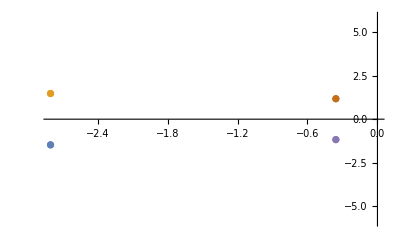

```mathematica
poles=ReIm[Values[Solve[Denominator[tsumsub] == 0,s]]]
ListPlot[poles/.{Subscript[K, p]-> -88, Subscript[K, i]-> -100,Subscript[J, p]->10, Subscript[J, i]-> 56, Subscript[K, t]-> -0.1}]
```

```mathematica
(*Sweep values of kp and ki*)
f[Kp_,Ki_,Jp_,Ji_,Kt_] = ReIm[N[Values[Solve[Denominator[tsumsub /.{Subscript[K, p]->Kp,Subscript[K, i]->Ki,Subscript[J, p]->Jp, Subscript[J, i]->Ji,Subscript[K, t]->Kt}]==0,s]]]]; (*returns list as s->[[values]]*) 
Manipulate[ListPlot[f[Kp,Ki,Jp,Ji,Kt]/.{Kp-> kp, Ki-> ki, Jp->jp, Ji-> ji, Kt->kt},AxesLabel->{"Real","Imaginary"},PlotStyle->PointSize[Large],PlotRange->{{-10,10},{-30,30}}],{kp,-100,100},{ki,-200,200},{jp,-50,50},{ji,-60, 60},{kt,-1,1}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
ClearAll["Global`*"]
```